## Useful functions

```mathematica
<<MaTeX`
texStyle={FontFamily->"Latin Modern Roman",FontSize->12,Magnification->1.6};
ParallelEvaluate[Off[General::munfl,FindFit::cvmit]];
Off[General::munfl,General::stop,LinearSolve::luc,FindFit::cvmit]
SetDirectory[NotebookDirectory[]]
```

/home/kirscher/kette_repo/31_resonances/code

```mathematica
RiccatiBesselJ[z_,l_]:=z SphericalBesselJ[l,z];
RiccatiBesselN[z_,l_]:=(-1.)^l z SphericalBesselY[l,z];
```

```mathematica
(*Boundery conditions for the wavefunction*)
alpha[ra_,ka_,la_,ha_]:=RiccatiBesselN[ka (ra+ha),la]/RiccatiBesselN[ka ra,la]

beta[rb_,kb_,lb_,hb_]:=RiccatiBesselJ[kb (rb+hb),lb]-RiccatiBesselJ[kb rb,lb] (RiccatiBesselN[kb (rb+hb),lb]/RiccatiBesselN[kb rb,lb])
```

LEC=(Λ,a_(3-1)^(S-wave) [fm],C_(2-body) [MeV],C_(3-body) [MeV])
the triton-proton S-wave scattering length is used to calibrate the core parameter and
was obtained by R. Lazauskas.

```mathematica
(* Nuclear E2=2.22 E3=8.48 ℏc=198*)
(* λ a0,r0 (Martin, 23) a1,r1 (Martin,45) a0 (Rimas, unprojected, 6) a1 (Rimas, unprojected, 7) a0 (Rimas, projected, 8) a1 (Rimas, projected, 9)*)
a0a1NUCLmartinrimas=Import[NotebookDirectory[]<>"../data/a0-a1_nucl_Rimas-Martin.dat","Table"][[2;;]];
(* λ C0,D0 (Martin, 23) C0,D0 (Rimas, unprojected, 45) C0,Do (Rimas, projected, 67)*)
LECsNUCLmartinrimas=Import[NotebookDirectory[]<>"../data/LECs_nucl_Rimas-Martin.dat","Table"][[2;;]];
LECsUNITmartinrimas=Import[NotebookDirectory[]<>"../data/LECs_univ_Rimas-Martin.dat","Table"][[2;;]];

(*activeLEC=LECsNUCLmartinrimas[[All,{1,2,3}]];*)
activeLEC=LECsUNITmartinrimas[[All,{1,2,3}]];
```

(non)local resonating-group potentials from a 2- and 3-body contact interaction for TRIMER-FERMION (ABC-A)

W_(non-local) takes the Energy (e_) in [MeV]

```mathematica
NormTF[core_?ArrayQ]:=1./Sqrt[Total[Flatten[Table[core[[i]][[1]] core[[j]][[1]] (Pi/(core[[i]][[2]]+core[[j]][[2]]))^1.5,{i,Length[core]},{j,Length[core]}]]]];

VlocTF[r_,lam_,Cc_,Dd_,Aa_,Bb_]:=Block[{eta2,eta3,w2,w3},
eta2=2. Cc/(2. (Aa+Bb)(3. Aa+3. Bb+2. lam))^(3./2.);
w2=3. (Aa+Bb) lam/(3. (Aa+Bb)+2. lam);
eta3=Dd/(6. (Aa+Bb)^2+16. (Aa+Bb) lam+2. lam^2)^(3./2.);
w3=(3. (Aa+Bb) lam ((Aa+Bb)+2. lam)/(3. (Aa+Bb)^2+8. (Aa+Bb) lam+lam^2));
eta2 Exp[-w2 r^2]+eta3  Exp[-w3 r^2]
];

WnolocTF[r_,rp_,Ee_,lam_,Cc_,Dd_,Aa_,Bb_,Ll_,TwoMyOverHBsq_]:=Block[{zeta1,zeta2,zeta3,a1,b1,c1,a2,b2,c2,a3,b3,c3},
zeta1=(27./64.)(2 (Aa+Bb))^(-3./2.) (1./TwoMyOverHBsq);
a1=(Aa+9. Bb) 3./32.;
b1=(Aa+Bb) 9./16.;
c1=(9. Aa+Bb) 3./32.;

zeta2=-27./32. Cc/(2. (Aa+Bb)+lam)^(3./2.);
zeta3=-27./64. Dd/(2  (Aa+Bb)+5 lam)^(3./2.);

a2=3. (Aa^2+9. Bb^2+10. Aa Bb+(14. Aa+18. Bb) lam)/(16. (2. (Aa+Bb)+lam));
b2=18. (Aa+Bb) ((Aa+Bb)+2. lam)/(16. (2. (Aa+Bb)+lam));
c2=3. (9. Aa^2+Bb^2+10. Aa Bb+(6. Aa+2. Bb) lam)/(16. (2. (Aa+Bb)+lam));

a3=3. (Aa^2+9. Bb^2+10. Aa Bb+(16. Aa+36. Bb) lam+27. lam^2)/(16. (2. (Aa+Bb)+5. lam));
b3=18. ((Aa+Bb)^2+4. (Aa+Bb) lam+3. lam^2)/(16. (2. (Aa+Bb)+5. lam));
c3=3. (9. Aa^2+Bb^2+10. Aa Bb+(24. Aa+4. Bb) lam+3. lam^2)/(16. (2 (Aa+Bb)+5. lam));

-(4 Pi r rp) (
zeta1 Exp[-a1 r^2-c1 rp^2] ((-(4 a1^2 r^2+b1^2 rp^2-2 a1)+(Ll+1) Ll/r^2-TwoMyOverHBsq Ee) I^Ll  SphericalBesselJ[Ll,I b1 r rp]
-4 a1 b1 r rp Sum[(1-Ll^2+l^2) I^(l+1)/Sqrt[3] (2/Sqrt[5])^((Ll+l)/2) SphericalBesselJ[1+l,I b1 r rp],{l,-Ll,Ll}])
+I^Ll zeta2 SphericalBesselJ[Ll,I b2 r rp] Exp[-a2 r^2-c2 rp^2]
+I^Ll zeta3 SphericalBesselJ[Ll,I b3 r rp] Exp[-a3 r^2-c3 rp^2]
)
];
```

The function <SolveSecular> expects the variable <<momentum>> in  [fm^-1]
As  W_(non-local) takes the Energy (e_) in [MeV];
The core wave function is parametrized via the "a0={{c_1,α_1},{c_2,α_2},...,{c_N,α_N}}" array:
ϕ_core=(∑^N)_(i=1)c_i·e_^(-α_i/2∏_j (r^-)_j^2)

```mathematica
SolveSecular[Rdis_?NumberQ,Npoints_?NumberQ,momentum_?NumberQ,Lin_?NumberQ,lam_?NumberQ,c0_?NumberQ,d0_?NumberQ,a00_?ArrayQ,TwoMyOverHBsq_?NumberQ]:=Block[{hDif,Dmat,Kmat,Wmat,bcol,Amat,ucol,wf,tanDelta,usol,energyMeV,nff,cij},

hDif=Rdis/Npoints;
energyMeV=(momentum^2)/TwoMyOverHBsq;
Kmat=SparseArray[{Band[{1,1}]->-2,Band[{2,1}]->1,Band[{1,2}]->1},{Npoints,Npoints}];

normsqu=NormTF[a00]^2;

Wmat=ConstantArray[0,{Npoints,Npoints}];

prefac=(*(4 π)^1.5*)1.;
Do[
(*If[a00[[ii]][[1]] a00[[jj]][[1]]≠0,*)

cij=a00[[ii]][[1]] a00[[jj]][[1]] normsqu;

amat=DiagonalMatrix[Table[-hDif^2 TwoMyOverHBsq VlocTF[i hDif,lam,c0,d0,a00[[ii]][[2]],a00[[jj]][[2]]],{i,1,Npoints}]];

wmat=Table[-prefac hDif^3 TwoMyOverHBsq WnolocTF[i hDif,j hDif,energyMeV,lam,c0,d0,a00[[ii]][[2]],a00[[jj]][[2]],Lin,TwoMyOverHBsq],{i,1,Npoints},{j,1,Npoints}]; 
(*Print[(Chop[cij (amat+wmat)])[[1;;4,1;;4]]//MatrixForm];*)
Wmat=Wmat+cij (amat+wmat);

(*]*)
,{ii,1,Length[a00]},{jj,1,Length[a00]}];

Dmat=DiagonalMatrix[Table[hDif^2 (momentum^2-(Lin (Lin+1))/(i hDif)^2),{i,1,Npoints}]];

Amat=Kmat+Dmat+Wmat;

bcol=ConstantArray[0,Npoints];
ucol=Array[Subscript["u", ##]&,{Npoints}];

bcol⟦-1⟧=- beta[Rdis,momentum,Lin,hDif];
Amat⟦-1⟧⟦-1⟧=Amat⟦-1⟧⟦-1⟧+alpha[Rdis,momentum,Lin,hDif];

usol=LinearSolve[Amat,bcol];

tanDelta= (RiccatiBesselJ[momentum Rdis,Lin]/RiccatiBesselN[momentum Rdis,Lin])-(usol⟦-1⟧/RiccatiBesselN[momentum Rdis,Lin]);

tanDelta
]
```

numerical and physical parameters

```mathematica
nf={6,4}; (* number form for printing, only *)
k0FM=0.01;  (*initial momentum*)

hbar=197.327053;
Mm=938.92;
m1=3 Mm;m2=Mm;
μ=m1 m2/(m1+m2);
mh2=(2 μ)/(hbar)^2;
sy={"nuclear","unitary"}[[2]];
Print["E_0 = ",(k0FM hbar)^2/(2 μ)," MeV     ℏ^2/(2 SubscriptBox[μ, A = 4]) = ",hbar^2/(2 (Mm^2/(2 Mm)))," MeV·fm^2     ℏ^2/(2 SubscriptBox[μ, A = 2]) = ",1/mh2]
λRange=Range[1,Length[activeLEC]];
```

E_0 = 0.00276473 MeV     ℏ^2/(2 SubscriptBox[μ, A = 4]) = 41.471 MeV·fm^2     ℏ^2/(2 SubscriptBox[μ, A = 2]) = 27.6473

```mathematica
GetP2lp1CotD[x_,l_,Energies_]:=Module[{localcore=x,locall=l,ErangeMeV=Energies},

core=localcore;

tanDs={};tanDp={};

SetSharedVariable[tanDs,tanDp];

ParallelDo[
momFM=Sqrt[mh2 energ];
TanDelSwave=SolveSecular[rr,nGrid,momFM,0,locall,C0,D0,core,mh2];
TanDelPwave=SolveSecular[rr,nGrid,momFM,1,locall,C0,D0,core,mh2];
AppendTo[tanDs,{Sqrt[mh2 energ],Sqrt[mh2 energ]/Chop[TanDelSwave]}];
AppendTo[tanDp,{Sqrt[mh2 energ],Sqrt[mh2 energ]^3/Chop[TanDelPwave]}];
,{energ,ErangeMeV}];

kCotDs=Reverse[Sort[tanDs,#1[[1]]>#2[[1]]&]]; (*Sort all the momentum since it is parallel*)
k3CotDp=Reverse[Sort[tanDp,#1[[1]]>#2[[1]]&]]; (*Sort all the momentum since it is parallel*)

{kCotDs,k3CotDp}
]
```

```mathematica
findLogDivisions[{xmin_,xmax_},n_Integer]:=10^FindDivisions[Log10@{xmin,xmax},n]

GetERE[x_,l_]:=Module[{localcore=x,locall=l},

core=localcore;

dataS={};dataP={};
tanDsL={};tanDpL={};
tanDs={};tanDp={};

SetSharedVariable[tanDs,tanDp];

ParallelDo[
momFM=Sqrt[mh2 energ];
TanDelSwave=SolveSecular[rr,nGrid,momFM,0,locall,C0,D0,core,mh2];
TanDelPwave=SolveSecular[rr,nGrid,momFM,1,locall,C0,D0,core,mh2];
AppendTo[tanDs,{energ,TanDelSwave}];
AppendTo[tanDp,{energ,TanDelPwave}];
,{energ,ErangeMeV}];

tanDs=Reverse[Sort[tanDs,#1[[1]]>#2[[1]]&]]; (*Sort all the momentum since it is parallel*)
tanDp=Reverse[Sort[tanDp,#1[[1]]>#2[[1]]&]]; (*Sort all the momentum since it is parallel*)
(*AppendTo[tanDsL,tnDs];
AppendTo[tanDpL,tnDp];*)
(*Extract the ERE Parameters*)
Lrel = 0;
dataS=Transpose[{Sqrt[mh2 ErangeMeV],Sqrt[mh2 ErangeMeV]/Re[tanDs⟦All,2⟧]}];
EreS=Fit[dataS⟦f1;;f2⟧,{1,p^2},p];
a0tf=-Coefficient[EreS,p,0]^-1;
r0tf= Coefficient[EreS,p,2]*2.;
Lrel = 1;
dataP=Transpose[{Sqrt[mh2 ErangeMeV],Sqrt[mh2 ErangeMeV]^3/Re[tanDp⟦All,2⟧]}];
EreP=Fit[dataP⟦f1;;f2⟧,{1,p^2},p];
a1tf=-Coefficient[EreP,p,0]^-1;
r1tf= Coefficient[EreP,p,2]*2.;
(*Print["dataS = ", dataS];*)
{a0tf,r0tf,a1tf,r1tf,dataS,dataP}
]
```

```mathematica
PlotERE:=Module[{},(*Plot the Phaseshifts for each α and C that I used*)
phaseS=Transpose[{tanDs⟦All,1⟧, ArcTan[tanDs⟦All,2⟧]}];
phaseP=Transpose[{tanDp⟦All,1⟧, ArcTan[tanDp⟦All,2⟧]}];
(*---------*)
Tfits=(Fit[dataS⟦1;;Min[10,Length[dataS]]⟧,{1,p^2,p^4},p]); (*fit ere again*)
dataTS=dataS;dataTS⟦All,2⟧=dataTS⟦All,2⟧^-1 ;
Polesp=(p/.NSolve[Tfits-ⅈ p==0,{p}]) ; (*find pole positions*) PolesE=hbar^2 Polesp^2 / (2 μ);
Print["S Pole Poitions in momentum: ", Polesp];
Print["S Pole Poitions in energy:   ", PolesE];
(*---------*)
Tfitp=(Fit[dataP⟦1;;Min[10,Length[dataP]]⟧,{1,p^2,p^4},p]); (*fit ere again*)
dataTP=dataP;dataTP⟦All,2⟧=dataTP⟦All,2⟧^-1 ;
Polepp=(p/.NSolve[Tfitp-ⅈ p^3==0,{p}]) ; (*find pole positions*) PolepE=hbar^2 Polepp^2 / (2 μ);
Print["P Pole Poitions in momentum: ", Polepp];
Print["P Pole Poitions in energy:   ", PolepE];
Print[Tfits];
Print[Tfitp];
GraphicsGrid[{{
Show[{ Plot[-(1/a0tf)+(1/2)r0tf k^2,{k,0,dataS⟦-1,1⟧}],ListPlot[dataS,PlotRange->{{dataS⟦1,1⟧,dataS⟦1,-1⟧},All}]},ImageSize->500,AxesLabel->{"E [MeV]","K CotTan[δ_(S - wave)] [fm^-1]"},PlotStyle->"Red", PlotLabel->" S-wave KCotδ compared with -1/a0+1/2r0 k^2"]
,
Show[{ Plot[-(1/a1tf)+(1/2)r1tf k^2,{k,0,dataP⟦-1,1⟧}],ListPlot[dataP,PlotRange->{{dataP⟦1,1⟧,dataP⟦1,-1⟧},All}]},ImageSize->500,AxesLabel->{"E [MeV]","K^3 CotTan[δ_(S - wave)] [fm^-3]"},PlotStyle->"Red",PlotLabel->" P-wave K^3Cotδ compared with -1/a0+1/2r0 k^2"]

},
{
Show[ListPlot[dataTS],Plot[Tfits^-1,{p,0,0.4},PlotRange->{Automatic,Automatic}],ImageSize->500,PlotLabel->"T matrix compared with the ERE^-1(O(k^4)) expansion"],
Show[ListPlot[dataTP],Plot[Tfitp^-1,{p,0,0.4},PlotRange->{Automatic,Automatic}],ImageSize->500,PlotLabel->"T matrix compared with the ERE^-1(O(k^4)) expansion"]

}
},ImageSize->1000]//Print
]
```

## Import density and fit wavefunctions

```mathematica
tailweight=0;
wflambdasN={1.0,2.0,3.0,4.0,6.0,8.0,10.0};
Martinϕnucl=Cases[Import["../data/abc_u_"<>ToString[NumberForm[#,{12,1}]]<>"_binf_r1b.dnst","Table"],{_?NumberQ,___}]&/@wflambdasN;
MϕN=Transpose[{#⟦All,1⟧,Sqrt[#⟦All,3⟧]}]&/@Martinϕnucl;
wflambdasU={1.5,2.0,3.0,4.0,6.0,8.0,10.0};
Martinϕunit=Cases[Import["../data/abc_univ_"<>ToString[NumberForm[#,{12,1}]]<>"_binf_r1b.dnst","Table"],{_?NumberQ,___}]&/@wflambdasU;
MϕU=Transpose[{#⟦All,1⟧,Sqrt[#⟦All,3⟧]}]&/@Martinϕunit;
If[sy=="unitary",
Mϕ=MϕU;
wflambdas=wflambdasU;
,
Mϕ=MϕN;
wflambdas=wflambdasN;]
```

λ=1.5  , core={{0.0207289,0.141276},{0.0709632,0.351648},{0.00213125,0.0554525},{0.131423,0.851405},{0.0812157,2.00756}}

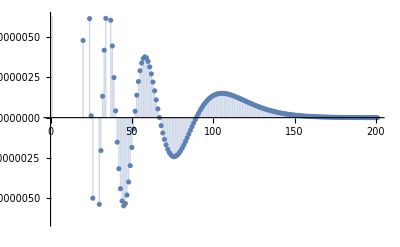

λ=2.  , core={{0.00449707,0.0693909},{0.127952,0.61019},{0.122021,2.20286},{0.0673087,1.46143},{0.0397175,0.204364}}

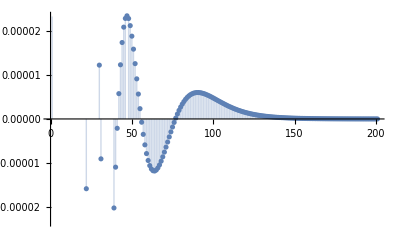

λ=3.  , core={{0.147644,0.825094},{0.0513337,0.293601},{0.000901115,0.0466721},{0.0116199,0.115381},{0.230533,2.69796}}

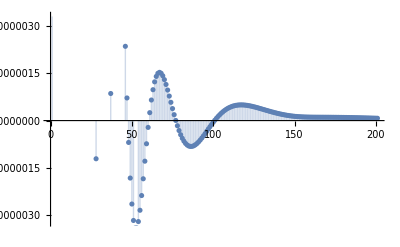

λ=4.  , core={{0.310622,2.6973},{0.0846594,0.651741},{0.0546782,0.690456},{0.00378499,0.0683166},{0.0355126,0.204023}}

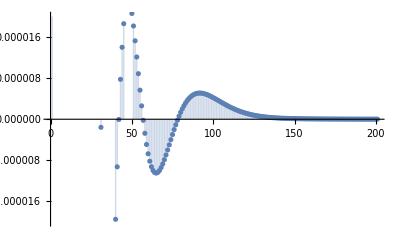

λ=6.  , core={{0.061183,0.563144},{0.390212,2.69989},{0.00226751,0.0596991},{0.0253878,0.170185},{0.061183,0.563144}}

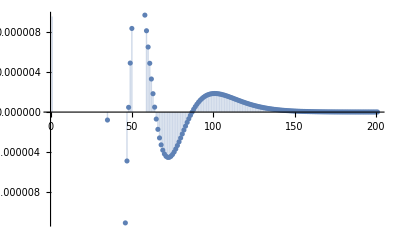

λ=8.  , core={{0.00160465,0.0549246},{0.0569949,0.515541},{0.0208755,0.153572},{0.0569949,0.515541},{0.431903,2.7}}

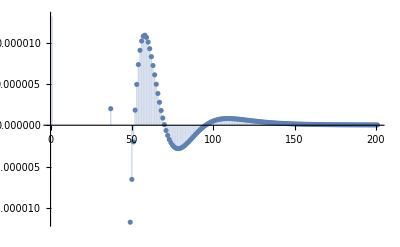

λ=10.  , core={{0.0543484,0.488247},{0.0012895,0.0529788},{0.0542877,0.488277},{0.460306,2.69973},{0.0182128,0.144591}}

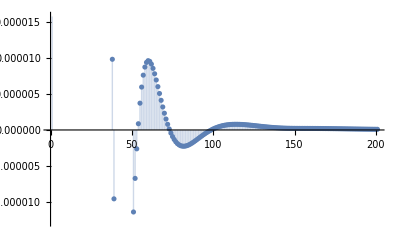

```mathematica
nk=5;

rmip=0.0;
rmap=21;

wfCores={};
wfs={};
w1=1;
amax=10^2;amin=0;
bmin=0.0;bmax=2.7;
w2=Min[Length[#]&/@Mϕ];
Do[
data=Mϕ[[ll]][[w1;;w2]];

modelGauss={Sum[aLn@i Exp[-bLn@i rrel^2],{i,nk}],Table[{amin<aLn@i <amax,bmin<bLn@i <bmax},{i,nk}]};
nlmLABC=NonlinearModelFit[data,modelGauss,Flatten[Table[{{aLn@i,RandomReal[{-0.1,0.1}]},{bLn@i,RandomReal[{0.0001,0.25}]}},{i,nk}],1],rrel,Weights->((#+1)^5&/@data[[All,1]])];
nlresi=nlmLABC["FitResiduals"];
(*modelGauss=Sum[aLn@i Exp[-bLn@i rrel^2],{i,nk}];
nlmLABC=NonlinearModelFit[data,modelGauss,Flatten[Table[{{aLn@i,RandomReal[{-10.1,10.1}]},{bLn@i,RandomReal[{0.0001,0.25}]}},{i,nk}],1],rrel];*)
basispara=Table[{aLn@i,bLn@i},{i,nk}]/.nlmLABC["BestFitParameters"];
AppendTo[wfCores,basispara];
AppendTo[wfs,Normal[nlmLABC]];

Print["λ=",wflambdas[[ll]],"  , core=",wfCores[[-1]]];
GraphicsGrid[{{
Show[ListLogLogPlot[Mϕ[[ll]],PlotLabel->"Λ = "<>ToString[wflambdas[[ll]]]<>" fm^-1"<>"  ;  f_fit=∑_(n = 1)^N c_n·e^(-SubscriptBox[α, n]·SuperscriptBox[ρ, 2]) with N="<>ToString[nk]<>"    Case: "<>ToString[sy]],
LogLogPlot[wfs[[-1]],{rrel,rmip,rmap},PlotLegends->{"original Ψ"},PlotRange->Full, AxesLabel->{"r [fm]","WaveFunction"}],ImageSize->Scaled[.8]],ListPlot[nlresi,Filling->Axis],
Plot[wfs[[-1]],{rrel,rmip,rmap},PlotLegends->{"original Ψ"},PlotRange->Full,Epilog->Map[Point,Mϕ[[ll]]], AxesLabel->{"r [fm]","WaveFunction"},ImageSize->Scaled[.8]]
}},ImageSize->{{1200},{1700}}]//Print
,{ll,Range[Length[wflambdas]]}];
```

## The real pudding

```mathematica
RefCoreN=Get[LocalObject["Reference_5Gauss_triton_Core_nuclear"]]
RefCoreU=Get[LocalObject["Reference_5Gauss_triton_Core_unitary"]]
RefPfm={0.00190,0.00338,0.00601,0.01069,0.01902,0.03382,0.06014,0.10695,0.19018,0.33820,0.60141,1.06948,1.90184};
```

{{{0.00305167,0.0411386},{0.0373942,0.438149},{0.0495568,0.201655},{0.0185,0.0960808},{0.0374061,0.438124}},{{0.0411953,0.772696},{0.0452758,0.821011},{0.0679986,0.236617},{0.0127357,0.0706551},{0.0466846,0.687197}},{{0.0540589,1.00405},{0.0542567,1.005},{0.0131114,0.0731049},{0.0789237,0.270866},{0.0539961,1.00526}},{{0.0597867,1.20017},{0.0597796,1.20017},{0.0597804,1.20017},{0.087039,0.303992},{0.0148695,0.0782339}},{{0.0028301,0.0444839},{0.0474994,0.402888},{0.0475008,0.402887},{0.191648,1.51569},{0.0252662,0.127875}},{{0.00304681,0.0456126},{0.0268268,0.133693},{0.10133,1.6888},{0.100398,0.431441},{0.102398,1.68891}},{{0.229307,1.69979},{0.00129516,0.0355028},{0.0201451,0.107625},{0.0492348,0.380576},{0.0492367,0.380573}}}

{{{0.0207289,0.141276},{0.0709632,0.351648},{0.00213125,0.0554525},{0.131423,0.851405},{0.0812157,2.00756}},{{0.00449707,0.0693909},{0.127952,0.61019},{0.122021,2.20286},{0.0673087,1.46143},{0.0397175,0.204364}},{{0.147644,0.825094},{0.0513337,0.293601},{0.000901115,0.0466721},{0.0116199,0.115381},{0.230533,2.69796}},{{0.310622,2.6973},{0.0846594,0.651741},{0.0546782,0.690456},{0.00378499,0.0683166},{0.0355126,0.204023}},{{0.061183,0.563144},{0.390212,2.69989},{0.00226751,0.0596991},{0.0253878,0.170185},{0.061183,0.563144}},{{0.00160465,0.0549246},{0.0569949,0.515541},{0.0208755,0.153572},{0.0569949,0.515541},{0.431903,2.7}},{{0.0543484,0.488247},{0.0012895,0.0529788},{0.0542877,0.488277},{0.460306,2.69973},{0.0182128,0.144591}}}

```mathematica
rGrid={22.4};(*Subdivide[22.5,32.1,2]*)
rr=rGrid[[1]];
EREs={};
lRange=Range[Length[wflambdas]];

nGrid=100;
f1=1;f2=4; (* How many momenta should be used to make ere?*)

k0FMin=0.02;
k0FMax=0.25;
Divisions=6;
rmip=0.0;
rmap=16;
(*---------------------*)
(*ErangeMeV=Subdivide[k0FMin^2/mh2,k0FMax^2/mh2,Divisions];*)(*N[findLogDivisions[{k0FMin^2/mh2,k0FMax^2/mh2},Divisions]];*)
ErangeMeV=RefPfm^2/mh2;
Erange1onfm=Sqrt[mh2 ErangeMeV];
exportdataL={};
exportdataS={};
exportdataP={};
Do[
Do[
nn=Flatten[Position[activeLEC⟦All,1⟧,_?(#==wflambdas[[ll]]&)]]⟦1⟧;
λ=0.25 activeLEC⟦nn⟧⟦1⟧^2;
C0=activeLEC⟦nn⟧⟦2⟧;D0=activeLEC⟦nn⟧⟦3⟧;
mycore=wfCores[[ll]];
Print["nn=",nn,"  nwf=",ll,"  λ=",λ,"  C0=",C0,"  D0=",D0,"  core=",mycore];
TmpData=GetP2lp1CotD[mycore,λ,ErangeMeV];
AppendTo[exportdataL,λ];
AppendTo[exportdataS,TmpData[[1]][[All,2]]];
AppendTo[exportdataP,TmpData[[2]][[All,2]]];
exportdataMoM=TmpData[[2]][[All,1]];
,{ll,lRange}];
,{rr,rGrid}];

lline=Prepend[exportdataL,"k/lambda"]
sdata=Transpose[Prepend[exportdataS,exportdataMoM]];
outs=Prepend[sdata,lline]//MatrixForm
Export["/tmp/tmpS.dat",outs,"Table"];
pdata=Transpose[Prepend[exportdataP,exportdataMoM]];
outp=Prepend[pdata,lline]//MatrixForm
Export["/tmp/tmpP.dat",outp,"Table"];
```

nn=1  nwf=1  λ=0.5625  C0=-62.6076  D0=-13.365  core={{0.0207289,0.141276},{0.0709632,0.351648},{0.00213125,0.0554525},{0.131423,0.851405},{0.0812157,2.00756}}

nn=2  nwf=2  λ=1.  C0=-111.302  D0=8.462  core={{0.00449707,0.0693909},{0.127952,0.61019},{0.122021,2.20286},{0.0673087,1.46143},{0.0397175,0.204364}}

nn=3  nwf=3  λ=2.25  C0=-250.43  D0=123.178  core={{0.147644,0.825094},{0.0513337,0.293601},{0.000901115,0.0466721},{0.0116199,0.115381},{0.230533,2.69796}}

nn=4  nwf=4  λ=4.  C0=-445.21  D0=372.602  core={{0.310622,2.6973},{0.0846594,0.651741},{0.0546782,0.690456},{0.00378499,0.0683166},{0.0355126,0.204023}}

nn=5  nwf=5  λ=9.  C0=-1001.72  D0=1524.25  core={{0.061183,0.563144},{0.390212,2.69989},{0.00226751,0.0596991},{0.0253878,0.170185},{0.061183,0.563144}}

nn=6  nwf=6  λ=16.  C0=-1780.84  D0=4165.55  core={{0.00160465,0.0549246},{0.0569949,0.515541},{0.0208755,0.153572},{0.0569949,0.515541},{0.431903,2.7}}

nn=7  nwf=7  λ=25.  C0=-2782.56  D0=9491.9  core={{0.0543484,0.488247},{0.0012895,0.0529788},{0.0542877,0.488277},{0.460306,2.69973},{0.0182128,0.144591}}

{k/lambda,0.5625,1.,2.25,4.,9.,16.,25.}

(k/lambda | 0.5625 | 1. | 2.25 | 4. | 9. | 16. | 25.
0.0019 | -0.250328 | -0.266558 | -0.272863 | -0.285549 | -0.289697 | -0.293811 | -0.300667
0.00338 | -0.25032 | -0.266551 | -0.272857 | -0.285543 | -0.289692 | -0.293806 | -0.300663
0.00601 | -0.250297 | -0.266529 | -0.27284 | -0.285526 | -0.289676 | -0.293792 | -0.30065
0.01069 | -0.250223 | -0.266462 | -0.272784 | -0.28547 | -0.289627 | -0.293747 | -0.300609
0.01902 | -0.249988 | -0.266247 | -0.272609 | -0.285295 | -0.289471 | -0.293605 | -0.30048
0.03382 | -0.249247 | -0.265572 | -0.272057 | -0.284743 | -0.288979 | -0.293157 | -0.300073
0.06014 | -0.246914 | -0.263446 | -0.270328 | -0.283013 | -0.287443 | -0.291761 | -0.298805
0.10695 | -0.239617 | -0.25682 | -0.265 | -0.277675 | -0.282739 | -0.287508 | -0.294966
0.19018 | -0.217277 | -0.236728 | -0.249385 | -0.261983 | -0.269234 | -0.275517 | -0.284304
0.3382 | -0.156152 | -0.184616 | -0.213834 | -0.226945 | -0.242326 | -0.253745 | -0.266749
0.60141 | -0.106933 | -0.192304 | -0.266551 | -0.29938 | -0.332045 | -0.353665 | -0.377848
1.06948 | -31.6319 | -13.404 | -7.1486 | -5.44942 | -4.3245 | -3.92631 | -3.76601
1.90184 | 4.90764 | 4.91189 | 5.04 | 5.19457 | 5.46575 | 5.65666 | 5.79458)

(k/lambda | 0.5625 | 1. | 2.25 | 4. | 9. | 16. | 25.
0.0019 | 0.19047 | 0.247873 | 0.277693 | 0.35006 | 0.385307 | 0.413152 | 0.450717
0.00338 | 0.190484 | 0.247888 | 0.277713 | 0.350081 | 0.385332 | 0.41318 | 0.450747
0.00601 | 0.190527 | 0.247937 | 0.277778 | 0.350147 | 0.385411 | 0.413268 | 0.450842
0.01069 | 0.190664 | 0.24809 | 0.277982 | 0.350356 | 0.385661 | 0.413548 | 0.451145
0.01902 | 0.1911 | 0.24858 | 0.278635 | 0.351028 | 0.386462 | 0.414444 | 0.452116
0.03382 | 0.192499 | 0.250167 | 0.280747 | 0.353224 | 0.389086 | 0.417382 | 0.45531
0.06014 | 0.197125 | 0.255509 | 0.287846 | 0.360809 | 0.398167 | 0.427576 | 0.466481
0.10695 | 0.213014 | 0.274358 | 0.312962 | 0.388627 | 0.431697 | 0.465436 | 0.508443
0.19018 | 0.266331 | 0.337429 | 0.398626 | 0.482789 | 0.546818 | 0.596487 | 0.653988
0.3382 | 0.469172 | 0.578566 | 0.736701 | 0.85671 | 1.01987 | 1.1452 | 1.26687
0.60141 | 1.54023 | 1.93197 | 2.62449 | 3.18884 | 4.14268 | 4.90816 | 5.59805
1.06948 | 16.2508 | 22.5845 | 41.7286 | 77.475 | 1957.88 | -161.438 | -94.8863
1.90184 | -24.0079 | -24.1472 | -23.9658 | -23.7032 | -23.3323 | -23.0867 | -22.9186)

```mathematica
kCotS=Transpose[Import["/tmp/tmpS.dat","Data"][[2;;]][[All,2;;]]];
k3CotP=Transpose[Import["/tmp/tmpP.dat","Data"][[2;;]][[All,2;;]]];
cutoffs=Import["/tmp/tmpP.dat","Data"][[1]][[2;;]];
MomsFM=Import["/tmp/tmpP.dat","Data"][[All,1]][[2;;]];
REFkCotS=Transpose[Import["/home/kirscher/kette_repo/31_resonances/data/tmpS.dat","Data"][[2;;]][[All,3;;]]];
REFk3CotP=Transpose[Import["/home/kirscher/kette_repo/31_resonances/data/tmpP.dat","Data"][[2;;]][[All,3;;]]];
REFcutoffs=Import["/home/kirscher/kette_repo/31_resonances/data/tmpP.dat","Data"][[1]][[8;;]];
REFMomsFM=Import["/home/kirscher/kette_repo/31_resonances/data/tmpP.dat","Data"][[All,1]][[2;;]];
```

{{0.112238,1.8911,10.4181},0.112238+1.8911 p^2+10.4181 p^4}

a_1 = -8.9096              r_1 = 3.7822   v_1 = 10.4181

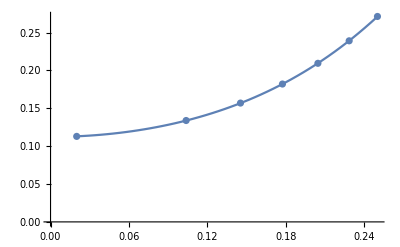

```mathematica
ll=1;
fitData=Transpose[{MomsFM,k3CotP[[ll]]}];
{ereParaP,Tfitp}=Fit[fitData⟦1;;Min[10,Length[fitData[[All,1]]]]⟧,{1,p^2,p^4},p,{"BestFitParameters","BestFit"}]
Print["a_1 = ",NumberForm[-1./ereParaP[[1]],nf],"              r_1 = ",NumberForm[2 ereParaP[[2]],nf],"   v_1 = ",NumberForm[ereParaP[[3]],nf]]
Show[ListPlot[fitData],Plot[Tfitp,{p,fitData[[All,1]][[1]],fitData[[All,1]][[-1]]}]]
```

```mathematica
Polepp=(p/.NSolve[Tfitp-ⅈ p^3==0,{p}]) 
PolepE=hbar^2 Polepp^2 / (2 μ)
```

{-0.112089-0.289063 ⅈ,0.+0.297987 ⅈ,0.+0.376126 ⅈ,0.112089-0.289063 ⅈ}

{-1.96278+1.7916 ⅈ,-2.45498+0. ⅈ,-3.91128+0. ⅈ,-1.96278-1.7916 ⅈ}

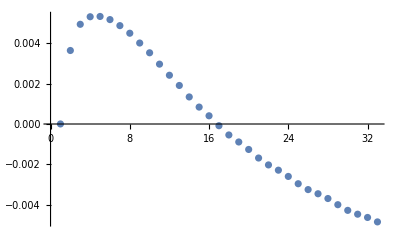

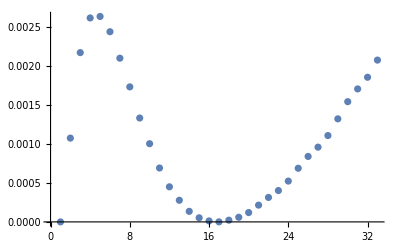

```mathematica
mom=dataP[[All,1]];
k3cotd=dataP[[All,2]];
Tmat=(4 Pi/938) mom[[#]]^3/(k3cotd[[#]]-I mom[[#]]^3)&/@Range[Length[mom]];
ListPlot[Re[Tmat]]
ListPlot[Im[Tmat]]
```

```mathematica
model=a+b/x+c/x^2;
l0=2;
lambdas=exportdata[[All,1]];
a0s=Transpose[{lambdas,exportdata[[All,4]]}];
fita0=model/.FindFit[a0s[[l0;;]],model,{a,b,c},x];
r0s=Transpose[{wflambdas,exportdata[[All,5]]}];
fitr0=model/.FindFit[r0s[[l0;;]],model,{a,b,c},x];
a1s=Transpose[{wflambdas,exportdata[[All,6]]}];
fita1=model/.FindFit[a1s[[l0;;]],model,{a,b,c},x];
r1s=Transpose[{wflambdas,exportdata[[All,7]]}];
fitr1=model/.FindFit[r1s[[l0;;]],model,{a,b,c},x];
legs="R_max="<>ToString[rr];
GraphicsGrid[{{
Show[ListPlot[a0s,PlotLegends->Placed[legs,Above],AxesLabel->{MaTeX["\\lambda [\\textrm{fm}^{-2}]",Magnification->2],MaTeX["a_S [\\textrm{fm}]",Magnification->2]},ImageSize->Large,PlotLabel->"lim _(λ → ∞) a_S = "<>ToString[Limit[fita0,x->Infinity]]<>" fm"],Plot[fita0,{x,0,lambdas[[-1]]},ImageSize->Large]],
Show[ListPlot[r0s,AxesLabel->{MaTeX["\\lambda [\\textrm{fm}^{-2}]",Magnification->2],MaTeX["r_S [\\textrm{fm}]",Magnification->2]},ImageSize->Large,PlotLabel->"lim _(λ → ∞) r_S = "<>ToString[Limit[fitr0,x->Infinity]]<>" fm"],Plot[fitr0,{x,0,10},ImageSize->Large]]
},{
Show[ListPlot[a1s,PlotLegends->Placed[legs,Above],AxesLabel->{MaTeX["\\lambda [\\textrm{fm}^{-2}]",Magnification->2],MaTeX["a_P [\\textrm{fm}^3]",Magnification->2]},ImageSize->Large,PlotLabel->"lim _(λ → ∞) a_P = "<>ToString[Limit[fita1,x->Infinity]]<>" fm^3"],Plot[fita1,{x,0,lambdas[[-1]]},ImageSize->Large]],
Show[ListPlot[r1s,AxesLabel->{MaTeX["\\lambda [\\textrm{fm}^{-2}]",Magnification->2],MaTeX["r_P [\\textrm{fm}^{-1}]",Magnification->2]},ImageSize->Large,PlotLabel->"lim _(λ → ∞) r_P = "<>ToString[Limit[fitr1,x->Infinity]]<>" fm^-1"],Plot[fitr1,{x,0,lambdas[[-1]]},ImageSize->Large]]
}}]
```

-Graphics-

```mathematica
ComplexPlot
```

```mathematica
cplxpoleSp=Transpose[{Re[exportdata[[All,8+#]]],Im[exportdata[[All,8+#]]]}]&/@{0,1,2,3};
cplxpolePp=Transpose[{Re[exportdata[[All,16+#]]],Im[exportdata[[All,16+#]]]}]&/@{0,1,2,3};
GraphicsGrid[{{
Show[ListPlot[#->exportdata[[All,1]],PlotRange->{{-0.5,0.5},{-0.5,0.5}},AxesLabel->{"Re[k_res] [fm^-1]","Im[k_res] [fm^-1]"}]&/@cplxpoleSp]
,
Show[ListPlot[#->exportdata[[All,1]],PlotRange->{{-0.5,0.5},{-0.5,0.5}},AxesLabel->{"Re[k_res] [fm^-1]","Im[k_res] [fm^-1]"}]&/@cplxpolePp]
}}
]
```

-Graphics-

```mathematica
nwf=7;
nn=Flatten[Position[activeLEC⟦All,1⟧,_?(#==wflambdas[[nwf]]&)]]⟦1⟧;
λ=0.25 activeLEC⟦nn⟧⟦1⟧^2;
C0=activeLEC⟦nn⟧⟦2⟧;D0=activeLEC⟦nn⟧⟦3⟧;
mycore=wfCores[[nwf]]
rprime=2.1;sca=1.;rMax=6;
eplot=ErangeMeV[[1]];
(*Plot[{WnolocTF[rMax,rprime,ErangeMeV[[2]],λ,C0,D0,mycore[[1]][[2]],mycore[[2]][[2]],0,mh2],WnolocTF[rMax,rprime,ErangeMeV[[2]],λ,sca C0,sca D0,mycore[[1]][[2]],mycore[[2]][[2]],1,mh2]},{rr,0.1,rMax},PlotRange->Full,PlotLegends->{"L_rel=0","L_rel=1"}]*)

GraphicsGrid[{{
Plot3D[{(*WnolocTF[rr,rp,ErangeMeV[[-1]],λ,sca C0,sca D0,mycore[[1]][[2]],mycore[[2]][[2]],1,mh2],*)WnolocTF[rr,rp,ErangeMeV[[-1]],λ,C0,D0,mycore[[1]][[2]],mycore[[1]][[2]],1,mh2]},{rr,0.1,rMax},{rp,0.1,rMax},PlotRange->Full,PlotLegends->{"E="<>ToString[eplot],"E="<>ToString[eplot]},PlotStyle->{Directive[Opacity[0.2],Orange, Specularity[White,50]],None},ImageSize->Scaled[.8]],Plot3D[{(*WnolocTF[rr,rp,ErangeMeV[[-1]],λ,sca C0,sca D0,mycore[[1]][[2]],mycore[[2]][[2]],1,mh2],*)WnolocTF[rr,rp,ErangeMeV[[-1]],λ,C0,D0,mycore[[2]][[2]],mycore[[2]][[2]],1,mh2]},{rr,0.1,rMax},{rp,0.1,rMax},PlotRange->Full,PlotLegends->{"E="<>ToString[eplot],"E="<>ToString[eplot]},PlotStyle->{Directive[Opacity[0.2],Orange, Specularity[White,50]],None},ImageSize->Scaled[.8]]},{
Plot3D[{(*WnolocTF[rr,rp,ErangeMeV[[-1]],λ,sca C0,sca D0,mycore[[1]][[2]],mycore[[2]][[2]],1,mh2],*)WnolocTF[rr,rp,ErangeMeV[[-1]],λ,C0,D0,mycore[[1]][[2]],mycore[[2]][[2]],1,mh2]},{rr,0.1,rMax},{rp,0.1,rMax},PlotRange->Full,PlotLegends->{"E="<>ToString[eplot],"E="<>ToString[eplot]},PlotStyle->{Directive[Opacity[0.2],Orange, Specularity[White,50]],None},ImageSize->Scaled[.8]],Plot3D[{(*WnolocTF[rr,rp,ErangeMeV[[-1]],λ,sca C0,sca D0,mycore[[1]][[2]],mycore[[2]][[2]],1,mh2],*)WnolocTF[rr,rp,ErangeMeV[[-1]],λ,C0,D0,mycore[[2]][[2]],mycore[[1]][[2]],1,mh2]},{rr,0.1,rMax},{rp,0.1,rMax},PlotRange->Full,PlotLegends->{"E="<>ToString[eplot],"E="<>ToString[eplot]},PlotStyle->{Directive[Opacity[0.2],Orange, Specularity[White,50]],None},ImageSize->Scaled[.8]]
}},ImageSize->Full]
λ
C0
D0
```

{{0.258496,1.45748},{0.0859085,0.218432}}

-Graphics-

25.

-2929.17

92495.